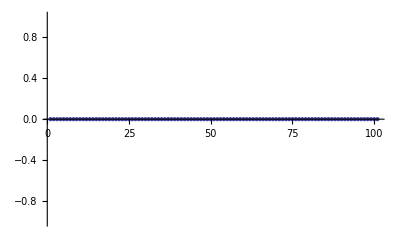

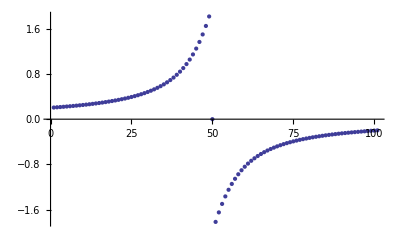

ListPlot::lpn: G2_data is not a list of numbers or pairs of numbers.

ListPlot[G2_data]

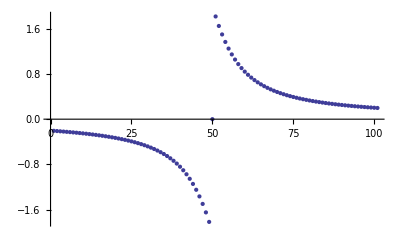

Fourier::nonopt: Options expected (instead of w) beyond position 2 in Fourier[G2_ω[i], i, w]. An option must be a rule or a list of rules.

Fourier[G2_ω[i],i,w]

```mathematica
β = 64;
U = 10;
μ = U/2;
t = 1/2;
Subscript[D, hb]= 2*t;
mf[n_Integer] := (2 π(n+1))/β;
Subscript[D̃, bethe][ζ_] :=2* (ζ-Sign[Im[ζ]]*√(Abs[ζ]^2-(2t)^2))/(2t)^2;
Subscript[G, ω][n_Integer] := (ⅈ*(mf[n] - Sign[mf[n]]*Sqrt[mf[n]^2+Subscript[D, hb]^2]))*2;

Subscript[G2, ω][n_Integer] := 2*(mf[n] - ⅈ(mf[n]- Sign[mf[n]]*√((mf[n])^2+(Subscript[D, hb])^2)));
ListPlot[Table[Re[Subscript[G, ω][i]],{i,-50,50}]]
ListPlot[Table[Im[Subscript[G, ω][i]],{i,-50,50}]]
ListPlot[Table[Re[Subscript[G2, ω][i]],{i,-50,50}]]
ListPlot[Table[Im[Subscript[G2, ω][i]],{i,-50,50}]]
Fourier[Subscript[G2, ω][i],i,w ]
```